[-Graphics-](https://github.com/Eltaurus-Lt/CnC/tree/main/Scripts)[-Graphics-](https://mipt.ru/education/chair/theoretical_mechanics/courses/haos-i-kotiki.php)[-Graphics-](https://t.me/miptdesign)-Graphics-mailto: efimov.ss@phystech.eduNonemailto: efimov.ss@phystech.eduHyperlinkHyperlinkActive

Пример экспорта ключевых кадров для последующего чтения скриптом в After Effects
Экспортируемая переменная должна быть либо одномерным списком (для произвольных одномерных параметров в AE), либо двумерным списком (для параметров Position, Scale и Orientation – длина второго измерения равна 2 для 2D слоёв и 3 для 3D слоёв)

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

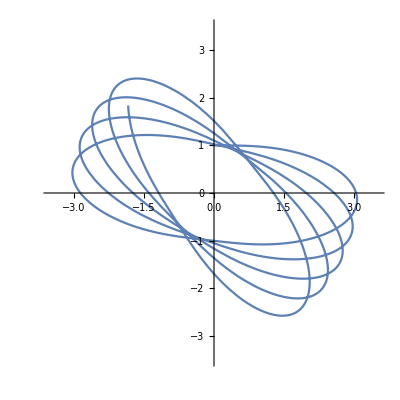

```mathematica
(*Решение дифференциального уравения (см. Семинар 1):*) 
F[r_]:=-1/r+1/r^2;
T=100; (*длина интервала интегрирования*)
sol=NDSolve[{x''[t]==F[r]*x[t]/r,x[0]==0, x'[0]==1, y''[t]==F[r]*y[t]/r,y[0]==1, y'[0]==0}/.{r-> √(x[t]^2+y[t]^2)},{x[t],y[t]},{t,0,T}]
ParametricPlot[{sol[[1,1,2]],sol[[1,2,2]]},{t,0,T},PlotRange->3.5{{-1,1},{-1,1}}]
```

```mathematica
(*Генерация ключевых кадров:*) 
Nframes=300; (*количество ключевых кадров*)
points={sol[[1,1,2]],sol[[1,2,2]]} /.t->#&/@Subdivide[0,T,Nframes-1];  (*спискок ключевых кадров*)
points//Dimensions (*проверка размерности списка*)
```

{300,2}

```mathematica
(*Экспорт в .txt:*) 
SetDirectory@NotebookDirectory[];
Export["WM to AE.txt",points,"table"];
```